## Darcy's Law

In the integral form, Darcy’s law, as refined by Morris Muskat, in the absence of gravitational forces and in a homogeneously permeable medium, is given by a simple proportionality relationship between the volumetric flow rate Q, and the pressure drop Δp through a porous medium. The proportionality constant is linked to the permeability k of the medium, the dynamic viscosity of the fluid μ, the given distance L over which the pressure drop is computed, and the cross-sectional area A.

```mathematica
volFlow[k_,A_,μ_,L_,dp_]:=(k A)/(μ L)dp
```

## Oxygen - Hemoglobin dissociation curve

```mathematica
Clear[bodyTempPoly,eqkO2,nHill,alphaO2,alphaCO2,k4Dyn,saO2ByPO2]
eqkO2[PO2_,PCO2_,T_,phpl_]:=Module[{P50,aO2,aCO2,cCO2,hp,h1,h2,h3,h4,k2,k3,k4,k22,k33,k55,k66},
P50=26.8;
aO2=alphaO2[T];
aCO2=alphaCO2[T];
cCO2=aCO2 PCO2;
k2=23.65;
k3=14.7;
k22=10^-6;
k33=10^-6;
k55=2.64 10^-8;
k66=1.56 10^-8;
hp=10^(-0.795phpl+1.357);
h1=1+k22/hp;
h2=1+k33/hp;
h3=1+hp/k55;
h4=1+hp/k66;
k4=k4Dyn[aO2,aCO2,PO2,PCO2,P50,{k2,k3},{h1,h2,h3,h4}](*2.03 10^5*);
k4(k3 cCO2 h2+h4)/(k2 cCO2 h1+h3)
]
nHill[PO2_]:=With[{
α=2.82,
β=1.20,
γ=29.25
},
α-β 10^(-PO2/γ)
]
bodyTempPoly[T_,{a0_,a1_,a2_}]:=a0+a1(T-37)+a2(T-37)^2
alphaO2[T_]:=bodyTempPoly[T,{1.37,-1.37 10^-2,5.80 10^-4}]10^-6/0.94
alphaCO2[T_]:=bodyTempPoly[T,{3.07,-5.7 10^-2,2 10^-3}]10^-5/0.94;
k4Dyn[aO2_,aCO2_,PO2_,PCO2_,P50_,{k2_,k3_},{h1_,h2_,h3_,h4_}]:=With[{
nH=nHill[PO2]
},
(aO2 PO2)^(nH-1)/(aO2 P50)^nH(k2 aCO2 PCO2 h1+h3)/(k3 aCO2 PCO2 h2+h4)
]
saO2ByPO2[PO2_,PCO2_,T_,phpl_]:=Module[{cCO2,k,q,a},
cCO2=alphaCO2[T]PCO2;
k=eqkO2[PO2,PCO2,T,phpl];
a=k cCO2;
a/(1+a)
]
```

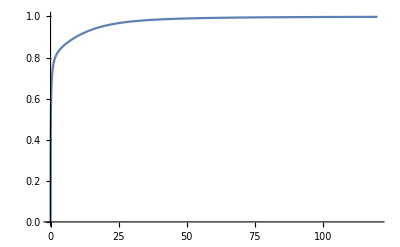

```mathematica
Plot[saO2ByPO2[PO2,40,37,7],{PO2,0,120},PlotRange->{0,1}]
```

```mathematica
alphaO2[37]
alphaCO2[37]
```

1.45745×10^-6

0.0000326596

```mathematica
saO2ByPO2[80,40]
```

0.995921

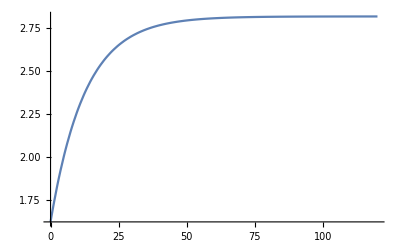

```mathematica
Plot[nHill[PO2],{PO2,0,120},PlotRange->All]
```

## Simple Model

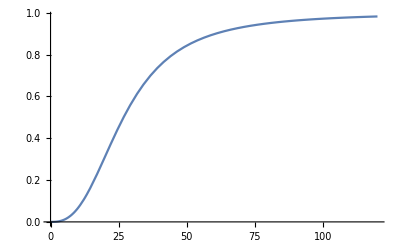

```mathematica
SO2Simple[PO2_]:=Module[{P50,n,q},
P50=26.8;
n=2.7;
q=(PO2/P50)^n;
q/(1.+q)
]
Plot[SO2Simple[PO2],{PO2,0,120}]
```

```mathematica
Solve[(p/p0)^n/(1+(p/p0)^n)==s,p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→p0 (-s/(-1+s))^(1/n)}}

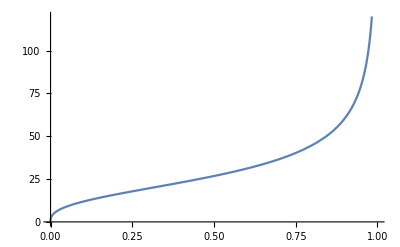

```mathematica
Clear[SO2SimpleInv]
SO2SimpleInv[S_]:=Module[{P50,n},
P50=26.8;
n=2.7;
P50(S/(1-S))^(1/n)
]
Plot[SO2SimpleInv[S],{S,0,1},PlotRange->{0,120}]
```

```mathematica
sat[p_,p0_]:=With[{a=(p/p0)^2.7},a/(1+a)]
oxygenContent[p_,hct_,α_,{P50_,Wpl_,Wrbc_,Hbrbc_}]:=((1-hct)Wpl+hct Wrbc)α p 32/1.429 100+4 hct Hbrbc sat[p,P50] 32/1.429/10
```

```mathematica
sat[100,26.8]
oxygenContent[p,hct,1.46 10^-6,{26.8,0.94,0.65,5.18}]
oxygenContent[100,0.45,1.46 10^-6,{26.8,0.94,0.65,5.18}]
```

0.97222

0.00326942 (0.94 (1-hct)+0.65 hct) p+(0.00646463 hct p^2.7)/(1+0.000139327 p^2.7)

20.5641

```mathematica
1.46 10^-6 100(*mol O2 / L blood*)
% 32(*g O2 / L blood*)
%/1.429(*L O2 / L blood*)
% 1000 /10(*ml O2 / dL blood*)
% 0.81(*corrected for blood water level*)
```

0.000146

0.004672

0.00326942

0.326942

0.264823

```mathematica
5.18/1000 64458/10(*RBC Hb g/dL*)
0.45%(*Blood Hb g/dL*)
```

33.3892

15.0252

```mathematica
32.0(*O2 molar mass g/mol*);
1.429(*O2 density g/L*);
64458.0(*Hb molar mass g/mol*);
4(*O2 per Hb*);
1/64458. 4 32./1.429 1000(*mL O2 / g Hb*)
```

1.38964

```mathematica
15.025159799999999 1.389635546581984
```

20.8795